```mathematica
(*Quit[]*)
```

```mathematica
1+1
```

2

```mathematica
Import["http://adsabs.harvard.edu/abs/1985A%26A...146..260E","HTML"]; (* Uncomment line above to get main reference for the method. 
Eriguchi,Y.;Mueller,E., Astronomy and Astrophysics (ISSN 0004-6361),vol.146,no.2,May 1985,p.260-268.
*)
```

```mathematica
(* conv -> convert rationals onto machine precision numbers; if you prefer to keep rationals, use ,,identity'' conv *)
```

```mathematica
$OperatingSystem
```

Unix

```mathematica
$HomeDirectory
```

/home/misiek

```mathematica
dir=If[$OperatingSystem=="Windows","H:\\misiek/RotatingStars/EM/SolidRotation/", "/home/misiek/RotatingStars/EM/SolidRotation/"]
```

/home/misiek/RotatingStars/EM/SolidRotation/

```mathematica
(*conv=(N[#]&)*)
```

```mathematica
conv=(# &)
```

#1&

```mathematica
NT=8(* angular rays (MAX NT=24 tested) *)
```

8

```mathematica
NR=8 (* radial slices, including surface, without center (MAX NR=32 tested ) *)
```

8

```mathematica
NL=8 (* number of Legendre polynomials (MAX NL=20 tested). WARNING: too large (e.g. NL=32) number of Legendere polynomials might cause numerical instability and catastrophic errors ! *)
```

8

```mathematica
R =Table[ToExpression["R"<>ToString[i]],{i,1,NT}];(* radius of the stellar surface *)
```

```mathematica
r=Table[j/NR*R[[i]],{i,1,NT},{j,1,NR}]//conv; (* discretized radial grid coordinates *)
```

```mathematica
Δr=Table[If[j==NR,0,R[[i]]/NR],{i,1,NT},{j,1,NR}]//conv;
(* trapezoidal integration rule, central point not included, surface weigth assumed ZERO *)
```

```mathematica
θ=Table[Pi/2*i/(NT-1),{i,0,NT-1}]//conv;   (* angular grid *)
```

```mathematica
Δθ=Join[{Pi/2/(NT-1)/2},Table[Pi/2/(NT-1),{i,2,NT-1}],{Pi/2/(NT-1)/2}] //conv;(* trapezoidal rule *)
```

```mathematica
(*surface=InterpolatingPolynomial[Transpose[{θ,R}],θθ]; (* interpolating polynomial representing surface *)*)
```

```mathematica
ρ=Table[
If[j==NR,0,ToExpression["ρ"<>ToString[i]<>"x"<>ToString[j]]
],{i,1,NT},{j,1,NR}] ;(* unknown densities at grid points; zero at surface *)
```

```mathematica
(* ρDISCR=Table[Join[{{0,ρC}},Table[{r[[i,j]],ρ[[i,j]]},{j,1,NR}]],{i,1,NT}];*)
```

```mathematica
(*ρINTERP=InterpolatingPolynomial[Table[{θ[[i]],InterpolatingPolynomial[ρDISCR[[i]],rr]//Simplify},{i,1,NT}],θθ];*)
```

```mathematica
Ω=(Ω0&) (*solid body rotation *)
```

Ω0&

```mathematica
(*Ω=(Ω0/(1+#^2/A^2)&)*) (* j-const rotation law *)
```

```mathematica
(*-Integrate[ζ Ω[ζ]^2,{ζ,0,x}]*)
```

```mathematica
(*Refine[%,x>0&&A>0]*)
```

```mathematica
ΦC=-1/2 #^2 Ω0^2& (* solid body rotation *)
```

-1/2 #1^2 Ω0^2&

```mathematica
(*ΦC=A^2Ω0^2/2/(1+#^2/A^2)-1/2 A^2 Ω0^2& (* centrifugal potential; normalized to zero at center ! *)*)
```

```mathematica
ΦC[0]
```

0

```mathematica
(*Limit[ΦC[x],x->Infinity]*)
```

```mathematica
kernel0[ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=
If[ra≥rb,
Sum[
rb^(2n)/ra^(2n+1)
LegendreP[2 n, Cosθa]*LegendreP[2n ,Cosθb],
{n,0,nLeg}],
Sum[
ra^(2n)/rb^(2n+1)
LegendreP[2 n, Cosθa]*LegendreP[2n ,Cosθb],
{n,0,nLeg}]
]
```

```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
DefaultCCompiler[]
```

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
$CCompiler
```

Automatic

```mathematica
Automatic
```

Automatic

```mathematica
$CCompiler=DefaultCCompiler[]
```

CCompilerDriver`GCCCompiler`GCCCompiler

```mathematica
part1=Sum[rb^(2n)/ra^(2n+1)
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part1NEW=part1//HornerForm;
```

```mathematica
part2=Sum[ra^(2n)/rb^(2n+1)
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part2NEW=part2//HornerForm;
```

```mathematica
part1Da=Sum[D[rb^(2n)/ra^(2n+1),ra]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part1Db=Sum[D[rb^(2n)/ra^(2n+1),rb]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part2Da=Sum[D[ra^(2n)/rb^(2n+1),ra]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
part2Db=Sum[D[ra^(2n)/rb^(2n+1),rb]
LegendreP[2 n, ca]*LegendreP[2n ,cb],
{n,0,NL}];
```

```mathematica
kernel5=Compile[{{ra,_Real},{ca,_Real},{rb,_Real},{cb,_Real}},
If[ra≥rb,Evaluate[part1]//Evaluate,Evaluate[part2]]//Evaluate,CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization"->False}
]; (* this kernel seems to be fastest; tested on Microsoft Visual Studio Compiler *)
```

```mathematica
kernel5Da=Compile[{{ra,_Real},{ca,_Real},{rb,_Real},{cb,_Real}},
If[ra≥rb,Evaluate[part1Da],Evaluate[part2Da]]//Evaluate,CompilationTarget->"C"
]; (* derivatives of the kernel *)
```

```mathematica
kernel5Db=Compile[{{ra,_Real},{ca,_Real},{rb,_Real},{cb,_Real}},
If[ra≥rb,Evaluate[part1Db],Evaluate[part2Db]]//Evaluate,CompilationTarget->"C"
];
```

```mathematica
kernel[ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=kernel5[ra,Cosθa,rb,Cosθb]
(* wrapper for convenient use within Mathematica; note that this slow down by a factor of two *)
```

```mathematica
Table[kernel0[9/10,4/10,3/10,1/10,2^nl],{nl,0,10,1}]//N
```

{1.12668,1.12616,1.12604,1.12604,1.12604,1.12604,1.12604,1.12604,1.12604,1.12604,1.12604}

```mathematica
kernel5[9/10,4/10,3/10,1/10]
```

1.12604

```mathematica
Do[kernel5@@Join[RandomReal[1,4]],{10000}]//Timing
```

{0.043683,Null}

```mathematica
Do[kernel0@@Join[RandomReal[1,4],{NL}],{10000}]//Timing
```

{0.62818,Null}

```mathematica
Derivative[1,0,0,0,0][kernel][ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=
kernel5Da[ra,Cosθa,rb,Cosθb]
(* derivatives of the kernel required for Jacobian generation *)
```

```mathematica
Derivative[0,0,1,0,0][kernel][ra_?NumericQ,Cosθa_?NumericQ,rb_?NumericQ,Cosθb_?NumericQ,nLeg_?NumericQ]:=
kernel5Db[ra,Cosθa,rb,Cosθb]
```

```mathematica
(*
start=AbsoluteTime[];
sysMAIN=Table[ρ[[i,j]]+ΦC[r[[i,j]]*Sin[θ[[i]]]]
-4 Pi G 
Sum[
Sin[θ[[l]]]Δθ[[l]]
Sum[
r[[l,m]]^2 Δr[[l,m]] *ρ[[l,m]] 
kernel[       r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL],
{m,1,NR}],
{l,1,NT}]==C
,
{i,1,NT},{j,1,NR}
]//Chop;
AbsoluteTime[]-start
*)
```

```mathematica
(*
start=AbsoluteTime[];
sysMAINa=Table[ρ[[i,j]]+ΦC[r[[i,j]]*Sin[θ[[i]]]]
-4 Pi G 
Sum[
Sin[θ[[l]]]Δθ[[l]] 
Sum[
r[[l,m]]^2 Δr[[l,m]] *ρ[[l,m]]
Sum[
f[ 2n, r[[i,j]],r[[l,m]]] 
LegendreP[2 n, Cos[θ[[i]]]]*LegendreP[2n ,Cos[θ[[l]]]],
{n,0,NL}],
{m,1,NR}],
{l,1,NT}]
==C
,
{i,1,NT},{j,1,NR}
];
AbsoluteTime[]-start
*)
```

```mathematica
(*
start=AbsoluteTime[];
sysMAINb=Table[ρ[[i,j]]+ΦC[r[[i,j]]*Sin[θ[[i]]]]-4 Pi G Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
f[ 2n, r[[i,j]],r[[l,m]]] 
LegendreP[2 n, Cos[θ[[i]]]]*LegendreP[2n ,Cos[θ[[l]]]]*ρ[[l,m]],
{n,0,NL},{l,1,NT},{m,1,NR}]==C
,
{i,1,NT},{j,1,NR}
];
AbsoluteTime[]-start
*)
```

```mathematica
vars=Join[R,DeleteCases[Flatten[ρ],0],{C,ρC,Ω0}] ;(* unknown variables: density, surface, central density, parameter of the rotation law, and constant C *)
```

```mathematica
(* kernel[ra_,θa_,rb_,θb_]:=
If[ra==0,

4Pi rb Sin[θb],

If[θa≠θb,
((4EllipticK[(4 ra rb Sin[θa] Sin[θb])/(ra^2+rb^2-2 ra rb Cos[θa+θb])])/(√(ra^2+rb^2-2 ra rb Cos[θa+θb]))+(4EllipticK[(4 ra rb Sin[θa] Sin[θb])/(ra^2+rb^2+2 ra rb Cos[θa-θb])])/(√(ra^2+rb^2+2 ra rb Cos[θa-θb])))rb^2 Sin[θb]
,0]
]*)
```

```mathematica
(* sysMAIN2=Table[ρ[[i,j]]+ΦC[r[[i,j]]*Sin[θ[[i]]]]-Sum[
Δθ[[l]]  Δr[[l,m]] 
*
kernel[r[[i,j]],θ[[i]],r[[l,m]],θ[[l]]]
*
ρ[[l,m]],
{l,2,NT},{m,1,NR-1}]==C
,
{i,1,NT},{j,1,NR}
];
*)
```

```mathematica
(* potencjal w centrum *)
```

```mathematica
Φ0=-4 Pi G Sum[Sin[θ[[l]]] Δθ[[l]] Sum[r[[l,m]]Δr[[l,m]] ρ[[l,m]],{m,1,NR}],{l,1,NT}];
(* gravitational potential at the center; NOTE: this is exact discretized formula, no Legendre expansion used *)
```

```mathematica
eq0=ρC+ΦC[0]+Φ0==C;(* center is treated separately *)
```

```mathematica
eqMASS=M==4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
*ρ[[l,m]],
{l,1,NT},{m,1,NR}];(* equation to set total mass *)
```

```mathematica
eqANGMOM=J==4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^4 Δr[[l,m]] 
*ρ[[l,m]]*
Ω[  r[[l,m]]Sin[θ[[l]]]],
{l,1,NT},{m,1,NR}] ;(* equation to set angular momentum *)
```

```mathematica
(*
NOTE: mass and angular momentu are driving parameters. Usually, one use poorly justified choice of parameters, like central density, central angular momentum or axis ratio. These sequences have at least the same mass and angular momentum: you can compare them. Comparison of structures with different mass and angular momentum is nonsense! *)
```

```mathematica
(* Left-hand side of equations (with -C ) *)
fLHS=
Function[Evaluate[vars],
Join[
{ρC+ΦC[0]+Φ0-C},{M-4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
*ρ[[l,m]],
{l,1,NT},{m,1,NR}]},{J-4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^4 Δr[[l,m]] 
*ρ[[l,m]]*
Ω[  r[[l,m]]Sin[θ[[l]]]],
{l,1,NT},{m,1,NR}]},
Table[ρ[[i,j]]+ΦC[r[[i,j]]*Sin[θ[[i]]]]-4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
kernel[ r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]
*ρ[[l,m]],
{l,1,NT},{m,1,NR}]-C
,
{i,1,NT},{j,1,NR}
]
]//Flatten
(*,RuntimeAttributes->{Listable},Parallelization->True,
,CompilationOptions->{"ExpressionOptimization"->True}, CompilationTarget->"C"*)
];
```

```mathematica
(* fLHS@@RandomReal[1,Length[vars]] *)
```

```mathematica
(* I have still troubles with Jacobian generation. Naively, you can just differentiate equations with respect to variables using symbolic capabilities of Mathematica. Unfortunately this is unusually slow. Below is slightly better approach with derived formulae for jacobian, but still generation time is proportional to (NT*NR)^3. Once Jacobian is generated, FindRoot solves system of equations in few steps, and few seconds. But you must do this once. Pre-calculated Jacobians are  stored on disk  for convenience *)
```

```mathematica
(* Jacobian generation starts. Skip if you prefer to use pre-calculated one. *)
```

```mathematica
drlmk=SparseArray@ParallelTable[D[r[[l,m]],vars[[k]]],{l,1,NT},{m,1,NR},{k,1,Length[vars]}]
```

SparseArray[<64>, {8, 8, 67}]

```mathematica
dΔrlmk=SparseArray@ParallelTable[D[Δr[[l,m]],vars[[k]]],{l,1,NT},{m,1,NR},{k,1,Length[vars]}]
```

SparseArray[<56>, {8, 8, 67}]

```mathematica
If[FileExistsQ[dir<>"dKlmijk_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m"],
dKlmijk=Import[dir<>"dKlmijk_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m"],
timer=AbsoluteTime[];
dKlmijk=
SparseArray@ParallelTable[
Derivative[1,0,0,0,0][kernel][r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]drlmk[[i,j,k]]
+
Derivative[0,0,1,0,0][kernel][r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]drlmk[[l,m,k]]
,{l,1,NT},{m,1,NR},{i,1,NT},{j,1,NR},{k,1,Length[vars]}];
AbsoluteTime[]-timer;
Export[dir<>"dKlmijk_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m",dKlmijk];
]
```

SparseArray[<7680>, {8, 8, 8, 8, 67}]

```mathematica
dρlmk=SparseArray@ParallelTable[D[ρ[[l,m]],vars[[k]]],{l,1,NT},{m,1,NR},{k,1,Length[vars]}]
```

SparseArray[<56>, {8, 8, 67}]

```mathematica
(*timer=AbsoluteTime[];
dlmijkNEW=SparseArray@ParallelTable[
2*r[[l,m]]*drlmk[[l,m,k]]*Δr[[l,m]]*kernel[r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]*ρ[[l,m]]
+
r[[l,m]]^2 dΔrlmk[[l,m,k]]* kernel[ r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]*ρ[[l,m]]
+
r[[l,m]]^2 Δr[[l,m]]*dKlmijk[[ l,m,i,j,k]]*ρ[[l,m]]
+
r[[l,m]]^2 Δr[[l,m]] kernel[ r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]*dρlmk[[l,m,k]]
, 
{l,1,NT},{m,1,NR},{i,1,NT},{j,1,NR},{k,1,Length[vars]}]
AbsoluteTime[]-timer*)
```

```mathematica
(*Export[dir<>"dlmijkNEW_"<>ToString[NT]<>"_"<>ToString[NR]<>".m",dlmijkNEW];*)
```

```mathematica
If[FileExistsQ[dir<>"dlmijkOLD_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m"],
dlmijkOLD=Import[dir<>"dlmijkOLD_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m"],
timer=AbsoluteTime[];
dlmijkOLD=SparseArray@ParallelTable[
D[
r[[l,m]]^2 Δr[[l,m]] 
kernel[ r[[i,j]],Cos[θ[[i]]],r[[l,m]],Cos[θ[[l]]],NL]
*ρ[[l,m]],
vars[[k]]
], (* D ends *)
{l,1,NT},{m,1,NR},{i,1,NT},{j,1,NR},{k,1,Length[vars]}];
AbsoluteTime[]-timer;
Export[dir<>"dlmijkOLD_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m",dlmijkOLD];
]
```

SparseArray[<10304>, {8, 8, 8, 8, 67}]

```mathematica
(*dlmijkOLD-dlmijkNEW//Simplify//Flatten//Tr*)
```

```mathematica
(*jac=Table[,{i,1,Length[vars]},{j,1,Length[vars]}];*)
```

```mathematica
(*totaltimer=AbsoluteTime[];
For[ii=1,ii≤Length[vars],ii++,
timer=AbsoluteTime[];
jac[[ii]]=ParallelTable[D[(fLHS@@vars)[[ii]],vars[[j]]],{j,1,Length[vars]}];
Print["Eq=",ii,"\tTime=",AbsoluteTime[]-timer,"\tTotal time=",AbsoluteTime[]-totaltimer];
]*)
```

```mathematica
(*timer=AbsoluteTime[];
jacPARTNEWa=ParallelTable[
Flatten@Table[
-D[C,vars[[k]]]
+
D[ρ[[i,j]],vars[[k]]]
+
D[ΦC[r[[i,j]]*Sin[θ[[i]]]],vars[[k]]]
(* end of NON-gravitational part *)
,
{i,1,NT},{j,1,NR}
],{k,1,Length[vars]}]//Transpose;
AbsoluteTime[]-timer*)
```

```mathematica
(*timer=AbsoluteTime[];
jacPARTNEWb=ParallelTable[
Flatten@Table[
-
4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] 
*
dlmijkOLD[[l,m,i,j,k]],
{l,1,NT},{m,1,NR}]
,
{i,1,NT},{j,1,NR}
],{k,1,Length[vars]}]//Transpose;
AbsoluteTime[]-timer*)
```

```mathematica
(*Export[dir<>"jacPARTNEWa_"<>ToString[NT]<>"_"<>ToString[NR]<>".m",jacPARTNEWa];*)
```

```mathematica
(*Export[dir<>"jacPARTNEWb_"<>ToString[NT]<>"_"<>ToString[NR]<>".m",jacPARTNEWb];*)
```

```mathematica
If[FileExistsQ[dir<>"jac_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m"],
jac=Import[dir<>"jac_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m"];,
timer=AbsoluteTime[];
jacPARTNEW=ParallelTable[
Flatten@Table[
-D[C,vars[[k]]]
+
D[ρ[[i,j]],vars[[k]]]
+
D[ΦC[r[[i,j]]*Sin[θ[[i]]]],vars[[k]]]
(* end of NON-gravitational part *)
-
4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] 
*
dlmijkOLD[[l,m,i,j,k]],
{l,1,NT},{m,1,NR}]
,
{i,1,NT},{j,1,NR}
],{k,1,Length[vars]}]//Transpose;
AbsoluteTime[]-timer;
jacCENTER=Table[
D[ ρC+ΦC[0]+Φ0-C,vars[[k]]    ]
,{k,1,Length[vars]}];
jacMASS=Table[
D[ M-4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^2 Δr[[l,m]] 
*ρ[[l,m]],
{l,1,NT},{m,1,NR}],vars[[k]]    ]
,{k,1,Length[vars]}];
jacANG=Table[D[J-4 Pi Sum[
Sin[θ[[l]]]Δθ[[l]] r[[l,m]]^4 Δr[[l,m]] 
*ρ[[l,m]]*
Ω[  r[[l,m]]Sin[θ[[l]]]],
{l,1,NT},{m,1,NR}],vars[[k]]
],{k,1,Length[vars]}];
jac=Join[{jacCENTER},{jacMASS},{jacANG},jacPARTNEW];
Export[dir<>"jac_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>".m",jac];
]
```

```mathematica
MaxMemoryUsed[]
```

99068888

```mathematica
(*jacPARTNEW=Import[dir<>"jacPARTNEWa_"<>ToString[NT]<>"_"<>ToString[NR]<>".m"]+Import[dir<>"jacPARTNEWb_"<>ToString[NT]<>"_"<>ToString[NR]<>".m"];*)
```

```mathematica
(*jacNEW=Import[dir<>"jac_"<>ToString[NT]<>"_"<>ToString[NR]<>".m"];*)
```

```mathematica
(*jacNEW[[1]]-jac[[1]]//Simplify*)
```

```mathematica
(*ParallelTable[If[jacNEW[[i,j]]!=0,1,0,LeafCount[jacNEW[[i,j]]]],{i,1, Length[vars],1},{j,1,Length[vars],1}]//MatrixPlot*)
```

```mathematica
(* Jacobian generation END here *)
```

```mathematica
(* Do[fLHS@@RandomReal[1,Length[vars]],{100}]//Timing*)
```

```mathematica
(* sys=Join[{eq0},{eqMASS},{eqANGMOM},sysMAIN]//Flatten//N;*)
```

```mathematica
(* sys=Join[{eq0},{eqMASS},{eqANGMOM},fLHS@@vars]//Flatten;*)
```

```mathematica
jac//ByteCount
```

13407168

```mathematica
Dimensions[jac]
```

{67,67}

```mathematica
Length[vars]
```

67

```mathematica
G=1 (* Gravitational constant *)
```

1

```mathematica
M=Sqrt[Pi]/2(* Lane-Emden with R=Sqrt[Pi]/2 radius and rhoC=1*)
```

(√π)/2

```mathematica
K=1/2
```

1/2

```mathematica
NT*NR+3 (* number of equations *)
```

67

```mathematica
Dimensions[vars] (* number of variables *)
```

{67}

```mathematica
(* init=RandomReal[1,NT*NR+2]*)
```

```mathematica
(* initial starting guess *)
```

```mathematica
h[ζ]/.DSolve[{1/ζ^2D[ζ^2 h'[ζ],ζ]+4 Pi G /2/K h[ζ]==0,h[0]==ρC,h'[0]==0},h[ζ],ζ][[1]]//ComplexExpand//Simplify (* initial values from Lane-Emden equation*)
```

(ρC Sin[2 √π ζ])/(2 √π ζ)

```mathematica
Simplify[%,G>0&&K>0]
```

(ρC Sin[2 √π ζ])/(2 √π ζ)

```mathematica
ρLE=Refine[%,G>0&&K>0]/.ρC->1
```

Sin[2 √π ζ]/(2 √π ζ)

```mathematica
Solve[2 √π ζ==Pi,ζ]
```

{{ζ→(√π)/2}}

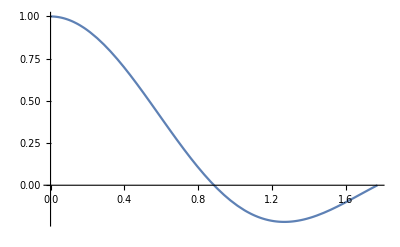

```mathematica
Plot[Sin[2 √π ζ]/(2 √π ζ),{ζ,0,Sqrt[Pi]}]
```

```mathematica
(*Solve[ρLE==0&&ζ>0,ζ,Reals]*)
```

```mathematica
Sqrt[K Pi/2/G]
```

(√π)/2

```mathematica
Integrate[4 Pi ζ^2 ρLE,{ζ,0,Sqrt[K Pi/2/G]}] (* MASS *)
```

(√π)/2

```mathematica
init2=Join[R/.(Rule[#,Sqrt[Pi]/2]&)/@R//N,Flatten[Table[ρLE/.ζ->r[[i,j]]/.(Rule[#,Sqrt[Pi]/2]&)/@R,{i,1,NT},{j,1,NR-1}],1]//N,{-1,Sqrt[Pi]/2,0}]//N;
%//Short
```

{0.886227,0.886227,0.886227,0.886227,«60»,-1.,0.886227,0.}

```mathematica
(*rozw=Import["E:\\temp\\EM\\Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_J_"<>ToString[N[0.499]]<>".m"];*)
```

```mathematica
(*init2=vars/.rozw(* use for RESTART ONLY ! *)*)
```

```mathematica
start=
If[FileExistsQ[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[0.0]]<>".m"],
Transpose[{vars,vars/.Import[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[0.0]]<>".m"]}],
Transpose[{vars,init2}]
]; (* starting guess *)
```

```mathematica
start=Transpose[{vars,init2}];
```

```mathematica
start[[1]]
```

{R1,0.886227}

```mathematica
J=0.0
```

0.

```mathematica
wynik=Block[{s = 0, e = 0, j = 0},{FindRoot[fLHS@@vars,start,MaxIterations->400,EvaluationMonitor:> e++, StepMonitor:> s++,
Method->{"Newton", "UpdateJacobian"->1},
Jacobian->{jac, EvaluationMonitor:> j++}]//Chop//AbsoluteTiming,{s,e,j}}];
```

```mathematica
wynik[[1,1]]
```

0.805485

```mathematica
wynik[[2]]
```

{3,4,4}

```mathematica
MaxMemoryUsed[]
```

110380872

```mathematica
ByteCount[jac]
```

13406720

```mathematica
Clear[J]
```

```mathematica
Clear[A]
```

```mathematica
For[J=0.0,J<=0.234,J=J+1/10,
(*For[A=1.02,A>0,A=A-1/1000,*)
timer=AbsoluteTime[];
If[!FileExistsQ[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[J]]<>".m"],
Block[{s = 0, e = 0, j = 0},{rozw,evals}={FindRoot[fLHS@@vars,start,MaxIterations->128,EvaluationMonitor:> e++, StepMonitor:> s++,Method->{"Newton", "UpdateJacobian"->1}, Jacobian->{jac, EvaluationMonitor:> j++}]//Chop,{s,e,j}}];
Export[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[J]]<>".m",rozw],
{rozw,evals}={Import[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[J]]<>".m"],{"From disk",0,0}}
];
initPREV=vars/.rozw;
start=Transpose[{vars,initPREV}];
Print["J=",N[J],"\t Time = ", AbsoluteTime[]-timer,"\n"];
Print["Evaluations=",evals[[2]],"\tStep=",evals[[1]],"\tJac=",evals[[3]]   ];
]
```

J=0.	 Time = 0.01428

Evaluations=0	Step=From disk	Jac=0

J=0.1	 Time = 0.01607

Evaluations=0	Step=From disk	Jac=0

J=0.2	 Time = 0.01129

Evaluations=0	Step=From disk	Jac=0

```mathematica
Jtest=0.2
```

0.2

```mathematica
rozw=Import[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[Jtest]<>".m"];
```

```mathematica
(*rozw=wynik[[1,2]];*)
```

```mathematica
pow=surface/.rozw//Expand;
```

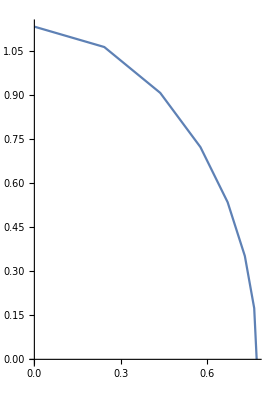

```mathematica
ListPolarPlot[Transpose[{θ,R}]/.rozw,InterpolationOrder->1,Joined->True]
```

```mathematica
Clear[dat]
```

```mathematica
dat[enum_]:=dat[enum]=Import[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[enum]]<>".m"]
```

```mathematica
dat[Jtest]//Short
```

{R1→0.770536,R2→0.781579,R3→0.809734,«62»,ρC→0.788971,Ω0→0.601724}

```mathematica
Clear[powSpline]
```

```mathematica
powSpline[enum_]:=powSpline[enum]=Interpolation[Transpose[{θ,R}]/.Import[dir<>"Solid_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_J_"<>ToString[N[enum]]<>".m"],InterpolationOrder->3,Method->"Hermite"]
```

```mathematica
powSpline[Jtest]
```

InterpolatingFunction[{{0., 1.5708}}, <>]

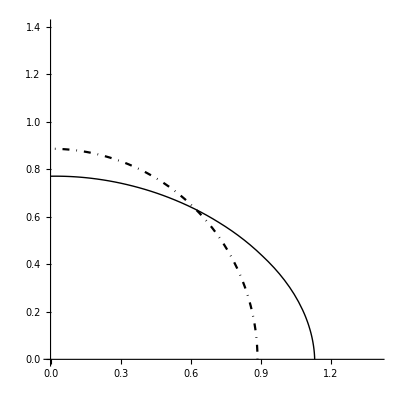

```mathematica
surf=PolarPlot[{powSpline[Jtest][Pi/2-θθ],Sqrt[Pi]/2},{θθ,0, Pi/2},AspectRatio->1,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,1.4},{0,1.4}}]
```

```mathematica
SetOptions[PolarPlot,AspectRatio->2/3,PlotStyle->{{Medium,Black},{Dotted,Black,Medium}},PlotRange->{{-1.5,1.5},{-1.0,1.0}}];
```

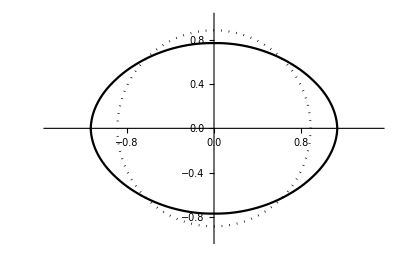

```mathematica
surfNEW=Show[PolarPlot[{powSpline[Jtest][Pi/2-θθ],Sqrt[Pi]/2},{θθ,0, Pi/2}] ,PolarPlot[{powSpline[Jtest][-Pi/2+θθ],Sqrt[Pi]/2},{θθ,Pi/2, Pi}] ,PolarPlot[{powSpline[Jtest][-θθ+3Pi/2],Sqrt[Pi]/2},{θθ,Pi,3 Pi/2}] ,PolarPlot[{powSpline[Jtest][-3/2Pi+θθ],Sqrt[Pi]/2},{θθ,3/2Pi, 2Pi}] ]
```

```mathematica
b=R[[1]]/.dat[Jtest]
```

0.770536

```mathematica
a=R[[-1]]/.dat[Jtest]
```

1.13113

```mathematica
b/a
```

0.681207

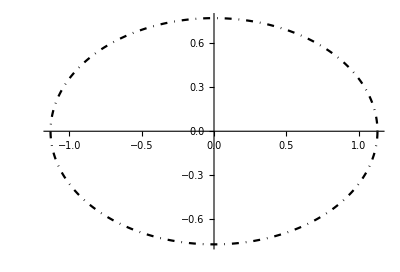

```mathematica
elipsa=ParametricPlot[{a Cos[t],b Sin[t]},{t,0,2Pi},PlotStyle->{{Normal,DotDashed,Black}}]
```

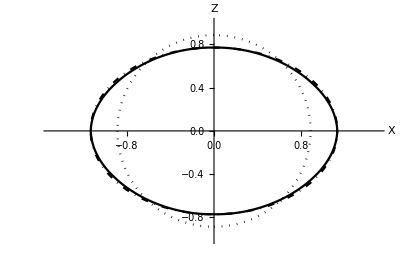

```mathematica
Show[surfNEW,elipsa,AxesLabel->{"X","Z"}]
```

```mathematica
Export[dir<>"Surface_0230.pdf",%]
```

/home/misiek/RotatingStars/EM/SolidRotation/Surface_0230.pdf

```mathematica
surface2=surface/.θθ->Pi/2-θθ;
```

```mathematica
surface2/.dat[0.0];
```

```mathematica
Simplify[%](* dlaczego to nie jest = const ??? *)
```

0.885496-0.0219712 θθ+0.670217 θθ^2-8.66425 θθ^3+63.81 θθ^4-302.884 θθ^5+988.661 θθ^6-2303.81 θθ^7+3913.93 θθ^8-4892.72 θθ^9+4494.9 θθ^10-2996.56 θθ^11+1409.46 θθ^12-443.183 θθ^13+83.5553 θθ^14-7.1391 θθ^15

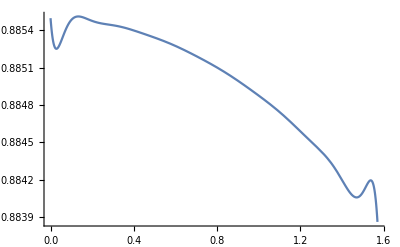

```mathematica
Plot[%,{θθ,0,Pi/2}]
```

```mathematica
Manipulate[
PolarPlot[{powSpline[i][Pi/2-θθ],Sqrt[Pi]/2},{θθ,0, Pi/2},AspectRatio->1/2,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,2.0},{0,1.0}},
PlotLabel->
"C="<>ToString[C/.dat[i]]<>", ρ_c="<>ToString[ρC/.dat[i]]<>", Ω_0="<>ToString[Ω0/.dat[i]]
],{{i,Jtest},0.0,0.246,0.1}]
```

```mathematica
ρDISP=Flatten[Table[
If[j≠0,
{θ[[i]],r[[i,j]],ρ[[i,j]]},{θ[[i]],0,ρC}
]
,{i,1,NT},{j,0,NR}]/.dat[Jtest],1]//Interpolation
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{0., 1.5708}, {0., 1.13113}}, <>]

```mathematica
ρDISPXY=ρDISP[θθ,rr]/.{rr->Sqrt[x^2+y^2],θθ->ArcTan[x/y]};
```

InterpolatingFunction::dmval: Input value {1.56689,1.14287} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.56884,1.14286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

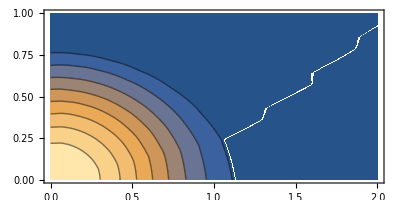

```mathematica
cp=ContourPlot[ρDISPXY*UnitStep[ρDISPXY],{x,0,2},{y,0,1},AspectRatio->1/2,PlotRange->All,Contours->{0.01,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}]
```

InterpolatingFunction::dmval: Input value {1.56856,1.14286} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.56968,1.14286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

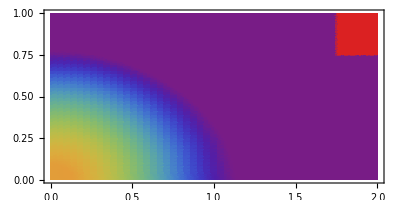

```mathematica
dp=DensityPlot[{ρDISPXY*UnitStep[ρDISPXY]+UnitStep[x-1.75]*UnitStep[y-0.75]},{x,0,2},{y,0,1},AspectRatio->1/2,PlotRange->{0,1},ColorFunction->"Rainbow",PlotPoints->50]
```

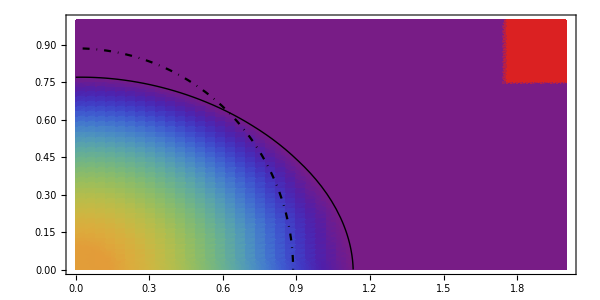

```mathematica
Show[dp,surf,ImageSize->600]
```

```mathematica
(*Export["H:\\misiek\\Articles\\SurfaceTracking\\figs\\j-const_A_02_J_02.png",%,ImageResolution->150]*)
```

```mathematica
Plot3D[ρDISPXY,{x,0,2.5},{y,0,2.5},AspectRatio->1,PlotRange->{0,All}]
```

-Graphics3D-

```mathematica
(*Manipulate[
ListContourPlot[
Join[{{0,0,ρC}},
Flatten[
Table[
{
r[[i,j]]*Sin[θ[[i]]],
r[[i,j]]*Cos[θ[[i]]],
If[j==NR,0,ρ[[i,j]]
]
},{i,1,NT},{j,1,NR}]
,1]
]
/.dat[j]
,AspectRatio->1/2,PlotRange->{{0,2},{0,1},{0,1}},InterpolationOrder->0,ColorFunction->"Rainbow",Mesh->All
],
{j,0.0,0.25,0.001}
]*)
```

```mathematica
{{NT,NR,NL},{C,Ω0,R[[1]],R[[-1]]}}/.dat[Jtest]
```

{{8,8,8},{-1.04017,0.601724,0.770536,1.13113}}

Import::nffil: File not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Import::nffil: File not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

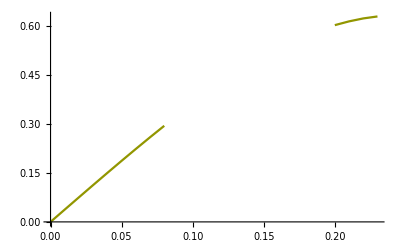

```mathematica
ListPlot[ Table[{j,Ω0}/.dat[j],{j,0.0,0.249,0.01}],Joined->True]
```

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

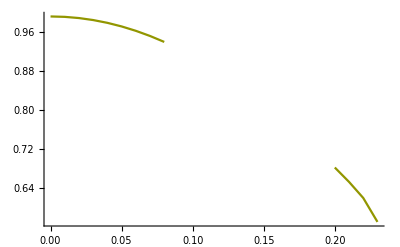

```mathematica
ListPlot[ Table[{j,R[[1]]/R[[-1]]}/.dat[j],{j,0.0,0.249,0.01}],Joined->True]
```

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

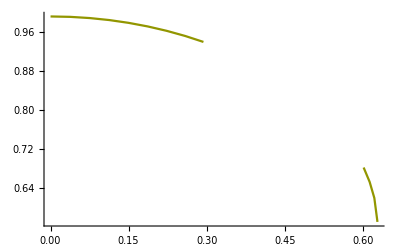

```mathematica
ListPlot[ Table[{Ω0,R[[1]]/R[[-1]]}/.dat[j],{j,0.0,0.249,0.01}],Joined->True]
```

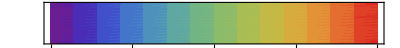

```mathematica
colorlabel=DensityPlot[x,{x,0,1},{y,0,1/20},ColorFunction->"Rainbow",AspectRatio->1/20,Frame->True,FrameTicks->{{None,None},{Automatic,None}}]
```

```mathematica
Manipulate[
Show[
ListDensityPlot[{{{1.9,0.0,1},{2,1,1}},
Join[{{0,0,ρC}},
Flatten[
Table[
{
r[[i,j]]*Sin[θ[[i]]],
r[[i,j]]*Cos[θ[[i]]],
If[j==NR,0,ρ[[i,j]]
]
},{i,1,NT},{j,1,NR}]
,1]
]
/.dat[jj]
}
,AspectRatio->1/2,PlotRange->{{0,2},{0,1},{0,1}},ColorFunction->"Rainbow",Mesh->False
]

,


Show@Table[ListPolarPlot[Table[{Pi/2-θ[[i]],r[[i,j]]},{i,1,NT}]/.dat[jj],Joined->True,InterpolationOrder->1,PlotStyle->{Thin,Black}],{j,1,NR}]
,
Show@Table[ListPolarPlot[{{0,0},{Pi/2-θ[[i]],r[[i,NR]]}}/.dat[jj],Joined->True,PlotStyle->{Thin,Black}],{i,1,NT}]
,
PolarPlot[{powSpline[jj][Pi/2-θθ],Sqrt[Pi]/2},{θθ,0, Pi/2},AspectRatio->1,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,1.5},{0,1.5}}

],
Frame->True,
FrameLabel->
"C="<>ToString[C/.dat[jj]]<>", ρ_c="<>ToString[ρC/.dat[jj]]<>", Ω_0="<>ToString[Ω0/.dat[jj]]
](*Show ends *)
,
{jj,0.0,0.235,0.001}
]
```

```mathematica
(*Manipulate[
ListPointPlot3D[
Join[{{0,0,ρC}},
Flatten[
Table[
{
r[[i,j]]*Sin[θ[[i]]],
r[[i,j]]*Cos[θ[[i]]],
If[j==NR,0,ρ[[i,j]]
]
},{i,1,NT},{j,1,NR}]
,1]
]
/.dat[j]
,AspectRatio->1/Sqrt[2],PlotRange->{{0,2},{0,1},{0,1}},ColorFunction->"Rainbow"
],
{j,0.0,0.299,0.001}
]*)
```

```mathematica
grid1=Show@Table[ListPolarPlot[Table[{Pi/2-θ[[i]],r[[i,j]]},{i,1,NT}]/.dat[Jtest],Joined->True,InterpolationOrder->1,PlotStyle->{Thin,Black}],{j,1,NR}];
```

```mathematica
grid2=Show@Table[ListPolarPlot[{{0,0},{Pi/2-θ[[i]],r[[i,NR]]}}/.dat[Jtest],Joined->True,PlotStyle->{Thin,Black}],{i,1,NT}];
```

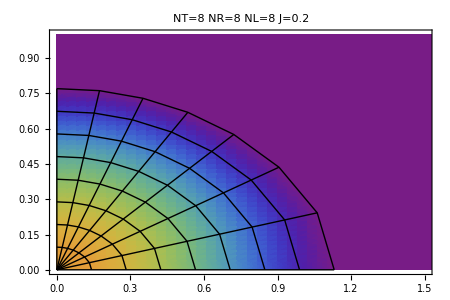

```mathematica
Show[dp,grid1,grid2,PlotLabel->"NT="<>ToString[NT]<>"\tNR="<>ToString[NR]<>"\tNL="<>ToString[NL]<>"\tJ="<>ToString[Jtest],ImageSize->450,PlotRange->{{0,1.5},{0,1}},AspectRatio->2/3]
```

```mathematica
R/.dat[Jtest]
```

{0.758587,0.761265,0.767523,0.779176,0.794776,0.815251,0.841069,0.872224,0.909191,0.952156,1.0015,1.05721,1.11887,1.18549,1.25179,1.28977}

```mathematica
For[jj=0.0,jj<=0.235,jj=jj+0.1,
frame=
GraphicsGrid[
{{
Show[
ListDensityPlot[{{{1.9,0.0,1},{2,1,1}},
Join[{{0,0,ρC}},
Flatten[
Table[
{
r[[i,j]]*Sin[θ[[i]]],
r[[i,j]]*Cos[θ[[i]]],
If[j==NR,0,ρ[[i,j]]
]
},{i,1,NT},{j,1,NR}]
,1]
]
/.dat[jj]
}
,AspectRatio->1/2,PlotRange->{{0,2},{0,1},{0,1}},ColorFunction->"Rainbow",Mesh->False
]

,


Show@Table[ListPolarPlot[Table[{Pi/2-θ[[i]],r[[i,j]]},{i,1,NT}]/.dat[jj],Joined->True,InterpolationOrder->1,PlotStyle->{Thin,Black}],{j,1,NR}]
,
Show@Table[ListPolarPlot[{{0,0},{Pi/2-θ[[i]],r[[i,NR]]}}/.dat[jj],Joined->True,PlotStyle->{Thin,Black}],{i,1,NT}]
,
PolarPlot[{powSpline[jj][Pi/2-θθ],Sqrt[Pi]/2},{θθ,0, Pi/2},AspectRatio->1,PlotStyle->{{Thick,Black},{DotDashed,Black}},PlotRange->{{0,1.5},{0,1.5}}

],
Frame->True,
FrameLabel->
"J="<>ToString[jj]<>", C="<>ToString[C/.dat[jj]]<>", ρ_c="<>ToString[ρC/.dat[jj]]<>", Ω_0="<>ToString[Ω0/.dat[jj]],ImageSize->450,
Epilog->Text["j-const, A=∞",{1.5,0.8}]
](*Show ends *)
},
{colorlabel}
}];(* GraphicsGrid ends *)
Export[dir<>"frames//frame_"<>ToString[NT]<>"_"<>ToString[NR]<>"_"<>ToString[NL]<>"_"<>ToString[10000+Rationalize[1000*jj]]<>".png",frame,ImageResolution->150];
Print["Frame ",ToString[Rationalize[1000*jj]]]
];
```

Frame 0

Frame 100

Frame 200